# Radioaktivität

Baddridschjia mist

```mathematica
ClearAll["Global`*"];
```

## Nulleffekt

```mathematica
N0 = 4577
```

4577

```mathematica
t0 = ((4*60)+42)*60+29
```

16949

```mathematica
U0=500
```

500

## Aufgabe 1

Co60

sU = 100 V

```mathematica
Us=370
```

370

## Aufgabe 2

```mathematica
n=6
```

6

```mathematica
t=10
```

10

```mathematica
j=n/t
```

3/5

```mathematica
t=n/j
```

10

```mathematica
n = {7, 13, 16, 21, 25, 29, 35, 42, 47, 53, 56, 59, 63, 69, 72, 79, 87, 89, 94, 99, 105, 108, 115, 118, 123, 130, 130, 135, 143, 149, 156, 162, 170, 172, 178, 186, 193, 195, 198, 200, 208, 210, 214, 220, 225, 238, 245, 250, 253, 257, 266, 272, 277, 279, 282, 287, 291, 296, 304, 308, 313, 315, 322, 327, 332, 335, 342, 349, 352, 361, 365, 371, 379, 383, 389, 393, 397, 403, 408, 414, 418, 428, 433, 439, 449, 455, 458, 463, 466, 472, 478, 479, 480, 485, 492, 497, 499, 503, 507, 509, 512, 520};
```

```mathematica
Length[n]
```

102

```mathematica
data=Table[n[[i+1]]-n[[i]], {i, 1, Length[n]-1}]
```

{6,3,5,4,4,6,7,5,6,3,3,4,6,3,7,8,2,5,5,6,3,7,3,5,7,0,5,8,6,7,6,8,2,6,8,7,2,3,2,8,2,4,6,5,13,7,5,3,4,9,6,5,2,3,5,4,5,8,4,5,2,7,5,5,3,7,7,3,9,4,6,8,4,6,4,4,6,5,6,4,10,5,6,10,6,3,5,3,6,6,1,1,5,7,5,2,4,4,2,3,8}

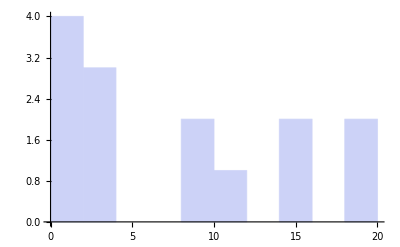

```mathematica
a=Histogram[BinCounts[data, {-0.5, 13.5, 1}], 10]
```

```mathematica
Mean[data]//N
```

5.07921

```mathematica
PDF[PoissonDistribution[30],k]
```

Piecewise[{{30^k/(ⅇ^30 k!), k≥0}, {0, True}}]

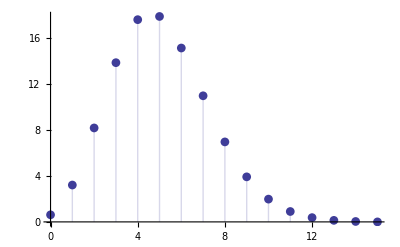

```mathematica
b = DiscretePlot[PDF[PoissonDistribution[Mean[data]],k]*102,{k,0,15},PlotRange->All,PlotMarkers->Automatic]
```

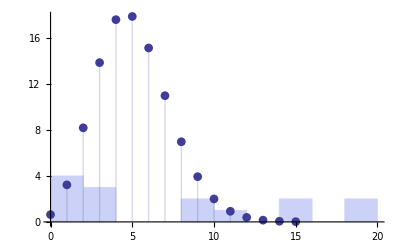

```mathematica
Show[a,b]
```

## Aufgabe 4

### 2

#### Ohne Abschirmung

```mathematica
U = 500
```

500

```mathematica
n = {1027, 985,1000,987, 979};
```

```mathematica
t = {6.28, 6.07, 6.18, 6.00, 6.00};
```

```mathematica
A = Mean[Table[n[[i]]/t[[i]], {i, 1, Length[n]}]]
```

163.057

#### 2mm Aluminium

```mathematica
n= {99};
```

```mathematica
t = {25.86};
```

```mathematica
A = Mean[Table[n[[i]]/t[[i]], {i, 1, Length[n]}]]
```

3.82831

#### 2mm Blei

```mathematica
n= {10, 10, 10, 10, 10};
```

```mathematica
t= {43.56, 29.24, 30.39, 29.54, 18.21};
```

```mathematica
A = Mean[Table[n[[i]]/t[[i]], {i, 1, Length[n]}]]
```

0.357659

```mathematica
A = 100/(5*60+13.73)
```

0.318745

### 3

#### ohne abschirmung

```mathematica
n=992;
```

```mathematica
t=2*60+18.50;
```

```mathematica
A=n/t
```

7.16245

#### 2mm blei

```mathematica
n=1004;
```

```mathematica
t=2*60+35.59;
```

```mathematica
A=n/t
```

6.45286

#### 10mm blei

```mathematica
n=1328;
```

```mathematica
t=5*60+6.43;
```

```mathematica
A=n/t
```

4.33378

#### 8mm

```mathematica
n=1065;
```

```mathematica
t=3*60+43.68;
```

```mathematica
A=n/t;
```

#### 6mm

```mathematica
n=1000;
```

```mathematica
t=3*60+11.50;
```

```mathematica
A=n/t
```

5.22193

#### 4mm

```mathematica
n=1000;
```

```mathematica
t=3*60+3.43;
```

```mathematica
A=n/t
```

5.45167

## Aufgabe 3

http://en.wikipedia.org/wiki/Uranium-238#Radium_series_.28or_uranium_series.29